# Основные принципы

## Принципы работы ядра

Структура выражений

## Нахождение головы выражения

Символ Head, применённый к выражению, выдаёт его голову. Но не стоит забывать про общий порядок вычислений: сначала вычисляется аргумент функции Head, а затем обрабатывается применение Head к этому аргументу. Примеры:

Упражнение: применить Head 1, 2, 3, 4 и 5 раз к следующему выражению и понять, почему получается такой результат:

```mathematica
f[][2+2][g[x]]
```

Сложно: использовать для этого функцию NestList.

```mathematica
NestList[Head,f[][2+2][g[x]],5]
```

{f[][4][g[x]],f[][4],f[],f,Symbol,Symbol}

Символы

## Неофициальная классификация

Системные символы начинаются с прописной (заглавной) буквы, значка доллара $ или некоторых спецсимволов (Table, Plot, N, $Assumptions, π, ⅇ). Для удобства рекомендуем в качестве своих символов использовать те, которые начинаются со строчной буквы (f, x1, tN0). Таким образом, по нашей неофициальной классификации есть два вида символов: системные и пользовательские.

## Первые системные символы: Plus и Times

В краткой форме применение Plus и Times записывается в привычном виде. При этом сохраняется общепринятый приоритет вычисления:

```mathematica
2+a*b
```

2+a b

При желании можно посмотреть полную форму вычисленного выражения с помощью функции FullForm (посмотрите документацию!) и убедиться в том, что это действительно краткая запись применения Plus и Times:

```mathematica
FullForm[2+a*b]
```

Plus[2,Times[a,b]]

Пропущенный значок умножения между элементарным выражением типа Real или Integer и любым другим выражением иного типа всё равно воспринимается как умножение.
Пробел, поставленный между двумя выражениями, всегда воспринимается Математикой как умножение и в некоторых случаях даже автоматически отображается как осветлённый знак умножения (крестик).
Например:

```mathematica
a b
```

a b

```mathematica
2 2
```

4

Но, понятно, что если вы не поставите ни значок умножения, ни пробел между двумя символами, которые хотите перемножить, то это будет воспринято как единый символ. Например, если вы хотите перемножить a и b, то в описанном случае WM воспримет введённое выражение как символ ab:

Помните, что самая существенная часть языка WM после изучения его основ — это изучение его системных символов. Подавляющее большинство из них подробнейшим образом описано в Документации. Начинайте изучать её уже сейчас!

Упражнение: изучить работу символов Print, List, Length, Range и Table. Узнать краткую форму записи применения List к произвольному (в т.ч. нулевому) количеству аргументов. После изучения этих символов переходите по ссылкам внизу страниц документации на страницы других символов и пытайтесь изучить их.

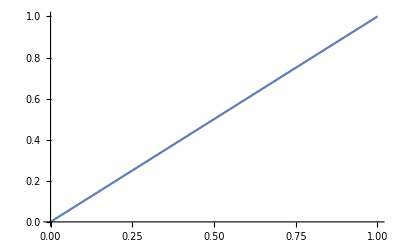

```mathematica
Plot[x,{x,0,1}]
```

Всё есть выражение!

Кстати, чтобы закомментировать выделенное выражение, нужно нажать “Alt” + “/”.

Способы применения функции:

```mathematica
f[x,y]
```

f[x,y]

```mathematica
x~f~y
```

f[x,y]

```mathematica
f@x
x//f
f[x]
```

f[x]

f[x]

f[x]

Вычисление выражений

Цель алгоритма — замена выражений. Работа алгоритма заключается в том, чтобы, постепенно заменяя выражения в определённом порядке, прийти к итоговому выражению, которое мы называем результатом вычисления. Суть ячейки вывода в том, что она повторяет написанное в ячейке ввода, только с учётом всех замен, сделанных алгоритмом.

```mathematica
f[x][g[x],7]
```

В исключительных случаях бывает так, что ячейка вывода даже не образуется. Это происходит тогда и только тогда, когда итоговым результатом вычисления выражения является символ Null:

```mathematica
x=5;
```

```mathematica
HoldForm@FullForm[x=5;]
```

CompoundExpression[Set[x,5],Null]

```mathematica
Null
```

А это краткий алгоритм вычисления выражения:

Здесь вы видите краткий алгоритм вычисления выражения ядром в рамках нашего курса. Как можно заметить, он рекурсивен. В нём используются термин «правила» и рассматривается возможность (или невозможность) их применения к выражениям, а также упоминаются «атрибуты» символов. Всё упомянутое в предыдущем предложении будет объяснено чуть позже.

Покажем на примере, как ядро вычисляет выражение: (2+2)*(3-4)→4*(3-4)→4*(-1)→-4

## Изменение порядка вычисления. Атрибуты символов

### Атрибуты символов

Любому символу могут быть поставлены в соответствие другие символы, которые называются атрибутами этого символа. Обычно атрибуты используются ядром для получения дополнительной информации о свойствах символа.

Список атрибутов (т.е. символ List, применённый к последовательности атрибутов как к аргументам) можно узнать, применив к интересующему символу функцию Attributes:

```mathematica
Attributes
```

Одним из наиболее часто используемых атрибутов является символ HoldAll. Наличие данного атрибута у символа-головы выражения убирает вычисление аргументов из алгоритма вычисления:

Например, атрибутом HoldAll обладает символ Hold:

```mathematica
Hold[2+2]
```

Hold[2+2]

```mathematica
Attributes@Hold
```

{HoldAll,Protected}

```mathematica
{1,2,f}*t
```

{t,2 t,f t}

```mathematica
Attributes@Times
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
1*f[u]
```

f[u]

Поэтому любое количество аргументов в выражении с головой Hold остаётся в невычисленном виде:

Из-за того, что Hold удерживает свои аргументы от вычисления, её удобно использовать, например, для просмотра полной формы (например, не 2+2, а Plus[2, 2]) сложных выражений:

```mathematica
FullForm
HoldForm
```

### Принудительное вычисление. Символ Evaluate

Атрибуты типа HoldAll можно обойти. Если нужно вычислить аргумент сложного выражения, который не должен быть вычислен из-за этих атрибутов, его можно обернуть в символ Evaluate:

```mathematica
Hold@Evaluate[2+2]
```

Hold[4]

Evaluate не может преодолеть только атрибут HoldAllComplete:

```mathematica
HoldComplete@Evaluate[2+2]
```

HoldComplete[Evaluate[2+2]]

## Домашнее задание

Построить функцию

```mathematica
x Boole@OddQ@Floor[15x]+Sin@x
```

по x от 0 до π. На примере этой функции подумайте, зачем символу Plot нужен атрибут HoldAll.

## Шаблоны

Понятия и простейшее использование

Шаблон — выражение определённой формы, задающее правило, по которому про любое выражение можно сказать, соответствует ли оно этому шаблону или нет.

```mathematica
MatchQ[45,f[_]*g[_]]
```

False

```mathematica
MatchQ[f@2*g@J@u[6,7],f[_]*g[_]]
```

True

```mathematica
MatchQ[f[2,7]*g@J@u[6,7],f[__]*g[_]]
```

True

Проверить, соответствует ли выражение шаблону, можно с помощью функции MatchQ. Первым аргументом у неё должно стоять выражение, для которого проверяется соответствие шаблону, а вторым — сам шаблон. MatchQ выдаёт символ True, если выражение подходит под шаблон, и символ False в противном случае.

Основные шаблоны

## Точные шаблоны

```mathematica
MatchQ[f@2*g@J@u[6,7],_@_*g[_]]
```

True

Это шаблоны, состоящие только из обычных выражений, и не используют собственно шаблонные конструкции. Т.е. любое обычное выражение может быть шаблоном, но это будет точный шаблон.

```mathematica
MatchQ[2,2]
```

True

MatchQ не сравнивает математически:

```mathematica
MatchQ[2,2.]
```

False

```mathematica
2===2.
```

False

```mathematica
f===_
```

False

## Универсальный шаблон Blank[]

Кроме точных шаблонов есть специальные шаблонные выражения. Например, Blank[].
Любое выражение удовлетворяет этому шаблону.

```mathematica
_//FullForm
```

Blank[]

```mathematica
MatchQ[a+b,HoldPattern[_+_]]
```

True

```mathematica
Attributes@HoldPattern
```

{HoldAll,Protected}

```mathematica
MatchQ[a+b,Hold[_+_]]
```

False

```mathematica
_+_
```

2 _

Из элементарных шаблонов можно сконструировать более сложные шаблоны:

```mathematica
k
```

## Указание головы выражения

Шаблону удовлетворяет любое выражение с заданной головой.

```mathematica
MatchQ[Integer[f,t],_Integer]
```

True

```mathematica
_Integer//FullForm
```

Blank[Integer]

## Именованные шаблоны «name:»

Шаблоны можно локально именовать, чтобы использовать в дополнительных условиях шаблона и некоторых других связанных объектах (об этом ниже). Именование шаблона не меняет его сути.

```mathematica
MatchQ[100,x_Integer/;x>10]
```

True

```mathematica
x
```

5

```mathematica
f[x_Integer]*g[y_Real]/;x>y
```

Именование может помочь при ненужном вычислении шаблонов:

```mathematica
MatchQ[a+b,x_+b_]
```

True

Именование записывается несколькими способами:

```mathematica
(x:(f@_Integer*g@_Real))*(y:7t)
```

## Дополнительные условия шаблонов

Нужен шаблон, удовлетворяющий любому выражению, строго большему 9.

Упражнение (на занятии). Привести несколько вариантов шаблона, которому удовлетворяют только листы длины 3. Какой из них удобнее использовать, если нужна длина не 3, а 1000?
Дополнительно: А если каждый элемент листа к тому же должен быть строкой?

```mathematica
MatchQ[Range@3,x_List/;Length@x==3]
```

True

```mathematica
MatchQ[{1,2,3},{_,_,_}]
```

```mathematica
MatchQ[{"a","b",c},x:{__String}/;Length@x==3]
```

False

```mathematica
MatchQ[{"a","b","c"},{Repeated[_String,{3}]}]
```

True

## *Шаблон BlankSequence и прочие

Это шаблон, удовлетворяющий последовательности любых выражений. Последовательность выражений не существует отдельно от шаблонных выражений.

```mathematica
__
___
```

```mathematica
MatchQ[f[],f[__]]
```

False

```mathematica
MatchQ[f[],f[___]]
```

True

```mathematica
Repeated
```

```mathematica
PatternTest
```

```mathematica
OddQ[3]
```

True

```mathematica
MatchQ[3,x_/;OddQ[x]]
```

True

```mathematica
MatchQ[3,_?OddQ]
```

True

## Полный и краткий вид шаблонов

Как сложение, умножение и многие другие объекты в WM, шаблоны можно записать в кратком виде. В таблице ниже показаны краткие формы распространённых шаблонов и их полные формы. В дальнейшем мы почти всегда будем использовать краткие формы шаблонов. Если вам встретился непонятный шаблон, в первую очередь узнавайте его полную форму.

```mathematica
patterns={_,x_,_h,_?f,x_?f,x_/;g[x]==1,x:_h?f/;g[x]==1};
Grid[
{Style[StringDelete[ToString@#,"("|")"],"Input"],FullForm@#}&/@patterns,
Alignment->{{"_","Blank[]"}},
Frame->All,
FrameStyle->LightGray
]
```

_ | Blank[]
x_ | Pattern[x,Blank[]]
_h | Blank[h]
_?f | PatternTest[Blank[],f]
x_?f | PatternTest[Pattern[x,Blank[]],f]
x_ /; g[x] == 1 | Condition[Pattern[x,Blank[]],Equal[g[x],1]]
x:_h?f /; g[x] == 1 | Condition[Pattern[x,PatternTest[Blank[h],f]],Equal[g[x],1]]

Упражнение: создать шаблон, которому удовлетворяют те элементы листа ниже, которые сами являются листами из двух и более чисел (NumberQ). Нужна функция Cases.

```mathematica
{{{},6},{},5,{x,y,z},{"1","2"},Table[Integrate[x^i,{x,1.,10.}],{i,10}]}
```

# Задание переменных и функций

## Правила замены

Replace и Rule «→»

Один из основных вариантов применения шаблонов — это замена выражения, удовлетворяющего шаблону, на другое выражение. Иными словами, происходит трансформация выражения на основании применения правил замены. Правило замены записывается с помощью символа Rule. Функционал замены всего выражения по правилу реализует функция Replace.

Здесь и далее при упоминании какого-либо нового системного символа ваша задача — прочитать о его применении в документации.

Наиболее часто используемый вид совместного применения функций Replace и Rule выглядит так:

```mathematica
Replace[expr,Rule[pattern,transformedExpr]](*эту ячейку не надо вычислять*)
```

```mathematica
Replace[59,_Integer->0]
Replace[f[x],_Integer->0]
```

0

f[5]

Rule можно записать в более удобном виде, что мы и будем делать в дальнейшем почти всегда:

```mathematica
Replace[expr,pattern->transformedExpr]
```

Такая стрелочка «->» часто автоматически преобразуется в «→»:

```mathematica
Replace[expr,pattern->transformedExpr]
```

expr — выражение, к которому мы хотим применить правила замены,
pattern — шаблон, который мы проверяем на предмет того, что expr ему удовлетворяет,
transformedExpr — результат вычисления всего выражения, если вычисленный expr удовлетворяет pattern’у.
Если вычисленный expr не удовлетворяет pattern’у, то результатом вычисления всего выражения будет вычисленный expr.

Если в шаблоне правила есть именованные части, то они могут быть использованы в transformedExpr:

```mathematica
Replace[y,t_Integer->t^2]
```

y

RuleDelayed «:>»

Правило можно задать не только с помощью функции Rule, но и RuleDelayed. Их различие заключается в различии набора их атрибутов:

```mathematica
_+_:>2+2
```

2 _:>2+2

У RuleDelayed есть атрибут HoldRest, который отсутствует у Rule. Он похож на атрибут HoldAll, но удерживает от вычисления не все аргументы, а все, кроме первого. В данном случае это значит, что при вычислении выражения, содержащего применение функции RuleDelayed, первый аргумент функции RuleDelayed, т.е. шаблон, вычислится, а второй, т.е. то, на что заменяется удовлетворяющее шаблону выражение, останется невычисленным.

Рассмотрим следующий пример. Пусть мы задали для символа t значение 4 (что это значит, рассмотрим позже):

```mathematica
t=4;
Replace[6,t_->t^2]
Replace[6,t_:>t^2]
```

16

36

Сравним теперь замену по обычному правилу (Rule) и по отложенному правилу замены (RuleDelayed). RuleDelayed[a,b] имеет краткую форму записи a:>b. При этом «:>» обычно автоматически превращается в «:>». Принудительно записать такой значок можно, нажав последовательно клавишу Esc, двоеточие, знак больше, клавишу Esc.

```mathematica
:>
->
```

Примеры применения.

Возвести в квадрат все чётные числа:

```mathematica
range=Range@10;
```

```mathematica
Replace[range,t_?EvenQ:>t^2,{1}]
```

{1,4,3,16,5,36,7,64,9,100}

```mathematica
range/.t_?EvenQ:>t^2
```

{1,4,3,16,5,36,7,64,9,100}

```mathematica
EvenQ@range
```

{False,True,False,True,False,True,False,True,False,True}

```mathematica
Attributes@EvenQ
```

{Listable,Protected}

*HoldPattern

```mathematica
MatchQ[a+b,_+_]
```

False

Странный результат, не правда ли? Символ a удовлетворяет шаблону Blank[], b тоже удовлетворяет Blank[]. Но здесь нужно вспомнить про последовательность вычисления выражений, из которой следует, что перед проверкой правил для всего выражения (т.е. проверки первого аргумента на соответствие шаблону — второму аргументу) сначала вычисляется a+b (и ничего не меняется, это подвыражение остаётся в том же виде), а вот затем вычисляется «_+_». У символа Plus есть правило, по которому n одинаковых его аргументов (назовём каждый из них x), которые могут стоять даже порознь друг от друга, заменяются на n*x. В нашем примере произошло это же самое:

```mathematica
_+_
```

2 _

Для того, чтобы избежать вычисления шаблонов, их можно оборачивать в символ HoldPattern. Это специальный шаблонный символ, который не учитывается при проверке соответствия выражения шаблону, а нужен только для избежания вычисления шаблона.

Итак, наш пример правильнее будет записать так:

```mathematica
MatchQ[a+b,HoldPattern[_+_]]
```

True